## Introduction to Mathematica

## 1. Basic Operations in R

```mathematica
x= 10
```

10

```mathematica
y= x/3+t
```

10/3+t

```mathematica
tarbutton = x+y
```

40/3+t

```mathematica
x=10
y=x/3+t
tarbutton = x + y
```

10

10/3+t

40/3+t

```mathematica
Clear[x]
Clear[y]
```

## 2. Plot Functions in Mathematica

We are now trying to make a nice plot in Mathematica displaying the following function:
 f(x) = x^3+ 2 x^2-x +10

```mathematica
plot1 = Plot[x^3 + 2 x^2 - x + 10,{x,-5,5},
GridLines->Automatic,
PlotLabel->"An example plot",
PlotStyle->{Dashed,Red}];
```

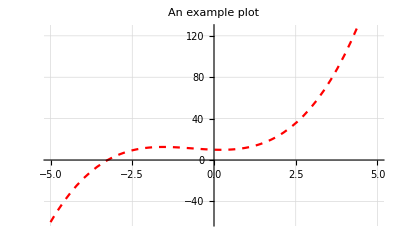

```mathematica
Show[plot1]
```

We can also export this plot. For that first set working directory and then use the export function. Notice how Mathematica automatically populates each directory!

```mathematica
SetDirectory["C:\\Users\\adeew\\OneDrive\\Documents\\GitHub\\R_Workshop\\tech_bootcamp"]
```

C:\Users\adeew\OneDrive\Documents\GitHub\R_Workshop\tech_bootcamp

```mathematica
Export["Example_Plot.jpg",plot1]
```

Example_Plot.jpg

## 3. Solve Equations and Systems of Equations

First consider a simple equation with one unknown variable:
3x + 10 = 1
We can solve this easily in Mathematica

```mathematica
Solve[3 x + 10  == 1]
```

{{x→-3}}

Now let’s consider a case where you have no numbers but only letters

```mathematica
Solve[α x + β == γ, x]
```

{{x→(-β+γ)/α}}

Solve can also deal with a systems of equations:
3x + 4y + 2z = -1
  x + 3y  -    z  = 10  
2x -   y +   4z =  8

```mathematica
Solve[{3x + 4y + 2z == -1,x +3y - z == 10,2x - y + 4z ==8},{x,y,z}]
```

{{x→271/5,y→-126/5,z→-157/5}}

## 4. How to Differentiate and Integrate

Mathematica is very helpful when dealing with integration and differentiation. Suppose we want to differentiate the following equation: f(x) = x^3+ 9x + 3

```mathematica
f1 = x^3 + 9x + 3
df1 = D[f1,x]
d2f1= D[f1,{x,2}]
```

3+9 x+x^3

9+3 x^2

6 x

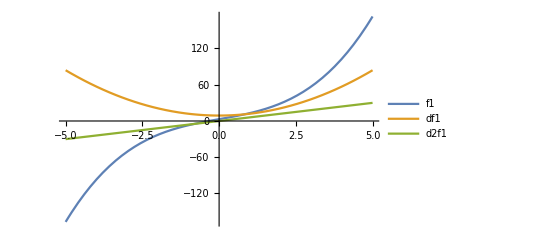

```mathematica
Plot[{f1,df1,d2f1},{x,-5,5},PlotLegends->"Expressions"]
```

It also easy to do partial derivatives. Consider the following function f(x) = 2x + 4xy + 8 y^3

```mathematica
f2 = 2x + 4 x y + 8y^3
D[f2,y]
D[f2,x]
```

2 x+4 x y+8 y^3

4 x+24 y^2

2+4 y

We can also estimate the integral ∫_1^5 x^3+ 9x + 3ⅆx

```mathematica
Integrate[f1,x]
Integrate[f1,{x,1,5}]
```

3 x+(9 x^2)/2+x^4/4

276

## 5. Find Minima and Maxima

There also built in techniques to help you find minima and maxima of functions

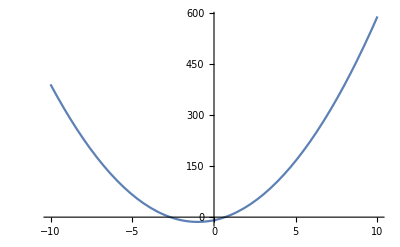

```mathematica
fMAX[x_] := 5x^2  + 10x -9
Plot[fMAX[x],{x,-10,10}]
```

```mathematica
Minimize[fMAX[x],x]
Maximize[fMAX[x],x]
```

{-14,{x→-1}}

Maximize::natt: The maximum is not attained at any point satisfying the given constraints.

{∞,{x→-∞}}

```mathematica
Solve[fMAX'[x]==0,x]
```

{{x→-1}}

We can do the same thing for constrained optimizations, i.e. in many instances your set of parameters is constrained and you want to account for that when optimizing the equation.
Consider the following issue:
Min     x^2+ 2y^2 
s.t     x + y >15 and x > 0 and y > 3

```mathematica
Minimize[{x^2+2 y^2,x+y > 15&&x > 0&&y > 6},{x,y}]
```

Minimize::wksol: Warning: there is no minimum in the region in which the objective function is defined and the constraints are satisfied; returning a result on the boundary.

{153,{x→9,y→6}}

## 6. Work with matrices

Matrix operations also work in Mathematica

```mathematica
mat1 = {{1,2,3},{5,6,7},{9,10,11}}
mat2 = {{1,0,0},{0,1,0},{0,0,1}}
MatrixForm[mat1]
MatrixForm[mat2]
```

{{1,2,3},{5,6,7},{9,10,11}}

{{1,0,0},{0,1,0},{0,0,1}}

(1 | 2 | 3
5 | 6 | 7
9 | 10 | 11)

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
MatrixForm[mat1*mat2]
MatrixForm[mat1 + mat2]
MatrixForm[Transpose[mat1]]
```

(1 | 0 | 0
0 | 6 | 0
0 | 0 | 11)

(2 | 2 | 3
5 | 7 | 7
9 | 10 | 12)

(1 | 5 | 9
2 | 6 | 10
3 | 7 | 11)